```mathematica
PrependTo[$Path,"C:/Users/ethan/OneDrive/Documents/Wolfram Mathematica"];
<< "GaussianIntegrals`"
```

```mathematica
IntInf[f_,intvar_:x]:=GaussianIntegral[f,intvar];
calcStats[f_,H_]:=Module[{fl2=f/Sqrt[IntInf[f^2]]},{N[IntInf[fl2*H[fl2]]],N[IntInf[x^2 f]],N[IntInf[x^4 f]]}]
calcStatsNoH[f_]:={N[IntInf[x^2 f]],N[IntInf[x^4 f]]}
reportStats[f_,H_]:=reportStats[calcStats[f,H]]
ToStringMod[x_]:=If[NumericQ[x]&&Im[x]==0&&x!=0&&Re[Log10[x]]<=-5,ToString[ScientificForm[x],TraditionalForm],ToString[x]]
reportStats[stats_]:="⟨x^2⟩ = "<>ToStringMod[stats[[2]]]<>"\n ⟨x^4⟩ = "<>ToStringMod[stats[[3]]]<>"\n ⟨H⟩ = "<>ToStringMod[stats[[1]]];
reportStatsComparison[stats_,comparison_]:=Module[{del={stats[[1]],stats[[2]]-comparison[[2]],stats[[3]]-comparison[[3]]}},"Δ⟨x^2⟩ = "<>ToStringMod[del[[2]]]<>"\nΔ⟨x^4⟩ = "<>ToStringMod[del[[3]]]<>"\n⟨H⟩ = "<>ToStringMod[del[[1]]]]
reportStatsComparison[f_,H_,comparison_]:=reportStatsComparison[calcStats[f,H],comparison]
Opsubs[Op_,subs_]:=(Op[#]/.subs)&
```

```mathematica
$Assumptions={a>0&&a∈Reals&&c∈Reals&&c>0&&Γ∈Reals&&Γ>0&&d∈Reals&&d>0&&x∈Reals&&t∈Reals&&t>0}
```

{a>0&&a∈ℝ&&c∈ℝ&&c>0&&Γ∈ℝ&&Γ>0&&d∈ℝ&&d>0&&x∈ℝ&&t∈ℝ&&t>0}

```mathematica
K[f_]:=(-a x+ c x^3) f+Γ D[f,x];
L[f_]:=D[K[f],x];
Ldag[f_]:=-(-a x+c x^3) D[f,x]+Γ D[f,{x,2}];
H[f_]:=Simplify[Ldag[L[f]]];
```

```mathematica
(*E P=L[P] steady-state equation*)
geneq=0==K[P[x]];
exact=DSolveValue[geneq,P[x],x];
exactnormed=exact/IntInf[exact]
exactstats=Join[{0},calcStatsNoH[exactnormed]];

(*geneq=FullSimplify[En P[x]==L[P[x]]]*)
```

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating ⅇ^(((a x^2)/2-(c x^4)/4)/Γ) 1 using Mathematica. Results may be slow.

(2 ⅇ^(-a^2/(8 c Γ)+((a x^2)/2-(c x^4)/4)/Γ))/(√(a/c) π (BesselI[-1/4,a^2/(8 c Γ)]+BesselI[1/4,a^2/(8 c Γ)]))

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating (2 √(a/c) c ⅇ^(-a^2/(8 c Γ)+(a x^2)/(2 Γ)-(c x^4)/(4 Γ)) x^2)/(a π (BesselI[-1/4,a^2/(8 c Γ)]+BesselI[1/4,a^2/(8 c Γ)])) using Mathematica. Results may be slow.

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating (2 √(a/c) c ⅇ^(-a^2/(8 c Γ)+(a x^2)/(2 Γ)-(c x^4)/(4 Γ)) x^4)/(a π (BesselI[-1/4,a^2/(8 c Γ)]+BesselI[1/4,a^2/(8 c Γ)])) using Mathematica. Results may be slow.

```mathematica
psi=Exp[-d x^2]/Sqrt[IntInf[Exp[-2d x^2]]]
```

d^(1/4) ⅇ^(-d x^2) (2/π)^(1/4)

```mathematica
Eresult=FullSimplify[IntInf[FullSimplify[psi*H[psi]]]]
```

(33 c^2-24 c d (a+2 d Γ)+48 d^2 (a+2 d Γ)^2)/(64 d^2)

```mathematica
dsol=Refine[Solve[D[Eresult,d]==0,d]][[1]]
```

{d→Root[-11 c^2+4 a c #1+32 a Γ #1^3+64 Γ^2 #1^4&,2]}

```mathematica
psifinal=Simplify[psi/.dsol];
psifinalnorm=psifinal/IntInf[psifinal]
```

(ⅇ^(-x^2 Root[-11 c^2+4 a c #1+32 a Γ #1^3+64 Γ^2 #1^4&,2]) √Root[-11 c^2+4 a c #1+32 a Γ #1^3+64 Γ^2 #1^4&,2])/(√π)

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating (8 ⅇ^(-25/8+5 x^2-x^4))/(5 π^2 (BesselI[-1/4,25/16]+BesselI[1/4,25/16])^2) using Mathematica. Results may be slow.

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating (2 √(2/5) ⅇ^(-25/16+(5 x^2)/2-x^4/2) x^2)/(π (BesselI[-1/4,25/16]+BesselI[1/4,25/16])) using Mathematica. Results may be slow.

GaussianIntegrals`Private`SingleGaussianIntegral::mathematica: Evaluating (2 √(2/5) ⅇ^(-25/16+(5 x^2)/2-x^4/2) x^4)/(π (BesselI[-1/4,25/16]+BesselI[1/4,25/16])) using Mathematica. Results may be slow.

General::stop: Further output of GaussianIntegrals`Private`SingleGaussianIntegral::mathematica will be suppressed during this calculation.

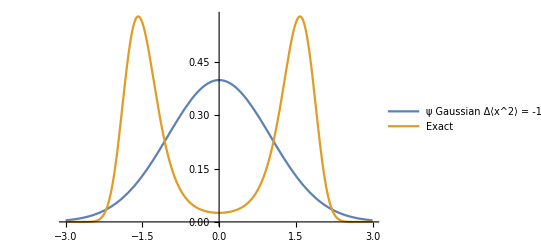

```mathematica
params={a->5,c->2,Γ->1};
toplot=psifinalnorm/.params;
exactparams=exactnormed/.params;
Hsubs=Opsubs[H,params];
exactstats=calcStats[exactparams,Hsubs];
Plot[{Legended[toplot,"ψ Gaussian\n"<>reportStatsComparison[toplot, Opsubs[H,params],exactstats]],Legended[exactparams,"Exact"]},{x,-3,3}]
```

```mathematica
GenFigure[psi_,params_,letter_]:=Module[{psisubs,plots,legends,stats},
psisubs=psi/.params;
plots={exactnormed/.params,psisubs};
stats=calcStats[psisubs,Opsubs[H,params]];
legends={"Exact","Gaussian\n"<>reportStatsComparison[stats,exactstats/.params]};
Show[{Plot[plots,{x,-5,5},PlotLegends->legends,PlotRange->Full,PlotLabel->"c = "<>ToString[c/.params]<>", Γ = "<>ToString[Γ/.params]],letter},ImageSize->All]
];
```

```mathematica
numij=3;
paramtable=Table[{a->4,c->2i+1,Γ->2j+1},{i,0,numij},{j,0,numij}];
lettertable=Table[Graphics[Style[Text["("<>(Alphabet[][[(numij+1)*i+j+1]])<>")",Scaled[{0.1,0.9}]],FontSize->15]],{i,0,numij},{j,0,numij}];
plotsoutput=GraphicsGrid[Table[GenFigure[psifinalnorm,paramtable[[i,j]],lettertable[[i,j]]],{i,1,numij+1},{j,1,numij+1}],ImageSize->340*Length[paramtable],Spacings->Scaled[0.01],ImageMargins->20]
```

General::munfl: Exp[-731.526] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1043.86] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Export["C:\\Users\\ethan\\OneDrive\\Documents\\Wolfram Mathematica\\Final versions for thesis\\Images\\Variational Cubic NegativeA.png",plotsoutput,"PNG"]
```

C:\Users\ethan\OneDrive\Documents\Wolfram Mathematica\Final versions for thesis\Images\Variational Cubic NegativeA.png

```mathematica
statsparams=Table[{a->10,c->2i+1,Γ->2j+1},{i,0,10},{j,0,10}];
dsols=N[dsol/.statsparams];
statspsis=psi/.dsols;
Hs=Table[IntInf[statspsis[[i,j]]Opsubs[H,statsparams[[i,j]]][statspsis[[i,j]]]],{i,1,11},{j,1,11}];
Hdata3D=MapThread[List,{c/.statsparams,Γ/.statsparams,Hs},2];
```

```mathematica
qm=NonlinearModelFit[Flatten[Hdata3D,1],b+mc c+mg g + mc2 c^2 + mg2 g^2+mcg c g,{b,mc,mg,mg2,mc2,mcg},{c,g}]
qm["RSquared"]
```

FittedModel[44.7132+6.90164 c-0.197286 c^2+6.90164 g+2.13034 c g-0.197286 g^2]

0.999865